```mathematica
μ = 12.2;
αtotal = 11.36;
r = αtotal/μ;
κ = 0.05;
```

```mathematica
shift=Table[RandomVariate[GammaDistribution[(1-κ)*αtotal, 1/r]],{i,1,100}];
```

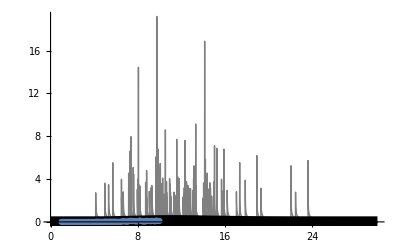

```mathematica
xvals=Range[1,10,0.1];
scaleval=2;
Show[
Plot[1/scaleval*PDF[GammaDistribution[κ*αtotal, 1/r],x-shift],{x,0,30}, PlotStyle->{Gray,Thin}, PlotRange->All],
Plot[PDF[GammaDistribution[αtotal, 1/r],x],{x,0,30}, PlotStyle->{Black,Thickness[0.02]}],
ListPlot[{
xvals,
Total[Table[PDF[GammaDistribution[κ*αtotal, 1/r], x-shift],{x,xvals}]ᵀ]/Length[shift]}ᵀ
]]
```

```mathematica
(√α)/β
```

(√α)/β

```mathematica
(√κα)/β
```

(√κα)/β

```mathematica
.5^2
```

0.25

```mathematica
0.1^2
```

0.01

```mathematica
Sqrt[0.5]
```

0.707107

```mathematica
SDpop = (√α)/β
```

(√α)/β

```mathematica
SDindiv=(√κα)/β
```

(√κα)/β

```mathematica
SDindiv = √κ SDpop
```

(0.223607 √α)/β

```mathematica
√k = 0.5
```

Set::write: Tag Sqrt in √0.25 is Protected.

0.5

```mathematica
k = 0.25
```

0.25